## DÚ 1 - Náhodné procházky - výsledky

## Import dat

```mathematica
𝕊aveFolder="data/"; (*Složka obsahující datové soubory*)

(*Názvy souborů s daty*)
𝔽ileNames={"1_ProstaProchazka_CtvercovyGrid","1_ProstaProchazka_TrojuhelnikovyGrid","1_ProstaProchazka_HexGrid","2_BezNavratu_CtvercovyGrid","2_BezNavratu_TrojuhelnikovyGrid","2_BezNavratu_HexGrid","3_BezPrekrizeni_CtvercovyGrid","3_BezPrekrizeni_TrojuhelnikovyGrid","3_BezPrekrizeni_HexGrid"};
nn=Length[𝔽ileNames];

(*Import dat*)
𝔻ata=Table[Import[NotebookDirectory[]<>𝕊aveFolder<>𝔽ileNames[[i]]<>".dat"][[2;;]],{i,1,nn}];
𝕃ogs=Table[Import[NotebookDirectory[]<>𝕊aveFolder<>𝔽ileNames[[i]]<>"_log.dat"],{i,1,nn}];


ℙlotData=Table[𝔻ata[[i]][[;;,{1,2}]],{i,1,nn}];
ℙlotDataPlusσ=Table[Table[{𝔻ata[[i]][[j,1]],𝔻ata[[i]][[j,2]]+𝔻ata[[i]][[j,3]]},{j,1,Length[𝔻ata[[i]]]}],{i,1,nn}];
ℙlotDataMinusσ=Table[Table[{𝔻ata[[i]][[j,1]],𝔻ata[[i]][[j,2]]-𝔻ata[[i]][[j,3]]},{j,1,Length[𝔻ata[[i]]]}],{i,1,nn}];

𝕊elfAvoidingWalkStat=Table[𝔻ata[[i]][[;;,{1,4,5,6}]],{i,7,nn}];
(*Fitování dat*)
𝔽its=Table[NonlinearModelFit[𝔻ata[[i]][[;;,{1,2}]],c*n^α,{c,α},n],{i,1,nn}];
```

## Zpracování dat

### Tabulka s výsledky

```mathematica
ℙrecision=3; (*počet desetinných míst, který se zobrazí v tabulce s výsledky*)

r1={{"Typ procházky","Mřížka","N","c","α"}};
c1={"prostá","prostá","prostá","bez návratu","bez návratu","bez návratu","bez překřížení","bez překřížení","bez překřížení"};
c2={"čtvercová","trojúhelníková","hexagonální","čtvercová","trojúhelníková","hexagonální","čtvercová","trojúhelníková","hexagonální"};

𝔻ividers={{{True}},{True,{True,False,False}}};

ℝesult=Table[{c1[[i]],c2[[i]],𝕃ogs[[i]][[1,3]],ToString[NumberForm[𝔽its[[i]][[1,2,1]][[1,2]],ℙrecision]]<>"±"<>ToString[NumberForm[𝔽its[[i]]["ParameterErrors"][[1]],ℙrecision]],ToString[NumberForm[𝔽its[[i]][[1,2,1]][[2,2]],ℙrecision]]<>"±"<>ToString[NumberForm[𝔽its[[i]]["ParameterErrors"][[2]],ℙrecision]]},{i,1,nn}];

ℝesult=Grid[Join[r1,ℝesult],Dividers->𝔻ividers];
```

### Globální nastavení grafů a tabulky s výsledky

```mathematica
𝔽ontSize=12;

ℙlotStyle={Red,Blue,Darker[Green]};
𝔽rameLabel={Style["n",𝔽ontSize],Rotate[Style["R",𝔽ontSize],-π/2]};
𝕀mageSize=500;

size=4.5;
ℙlotMarkers={{"●",size},{"●",size},{"●",size},{"▲",size},{"▲",size},{"▲",size},{"▲",size},{"▲"
,size},{"▲",size}};
t=0.003;
𝕃ineStyle={{Red,Thickness[t]},{Blue,Thickness[t]},{Darker[Green],Thickness[t]}};


𝔾raphs=ConstantArray[0,6];

xmin1=1; (*určuje plot range fitů*)
xmax1=10000;
ℙlotRange1=Full;
ℙlotRange1BezPrekrizeni={{1,120},Full};
temp={"Čtvercová mřížka: R","Trojúhelníkova mrížka: R","Hexagonální mřížka: R","Čtvercová mřížka: R±σ","Trojúhelníkova mrížka: R±σ","Hexagonální mřížka: R±σ"};
ℙointLegend1=PointLegend[{Red,Blue,Darker[Green],Red,Blue,Darker[Green]},temp,LegendMarkers->{"●","●","●","▲","▲","▲"}];
temp={"Čtvercová mřížka: fit","Trojúhelníkova mrížka: fit","Hexagonální mřížka: fit"};
𝕃ineLegend1=LineLegend[{Red,Blue,Darker[Green]},temp];
𝕊calingFunctions1={None,None};

xmin2=1;
xmax2=120;
ℙlotRange2={{xmin2,xmax2},{0,50}};
temp={"Prostá: R","Bez návratu: R","Bez překřížení: R","Prostá: R±σ","Bez návratu: R±σ","Bez překřížení: R±σ"};
ℙointLegend2=PointLegend[{Red,Blue,Darker[Green],Red,Blue,Darker[Green]},temp,LegendMarkers->{"●","●","●","▲","▲","▲"}];
temp={"Prostá: fit","Bez překřížení: fit","Bez návratu: fit"};
𝕃ineLegend2=LineLegend[{Red,Blue,Darker[Green]},temp];
𝕊calingFunctions2={None,None};
```

### Grafy - Srovnání různých procházek na stejné mřížce

#### Prosté náhodné procházky

```mathematica
(*Nastavení grafu*)
ℙlotLabel="Graf: Srovnání prostých náhodných procházek";(*Název grafu*)

𝔾raphNumber=1;
imin=1;
imax=3;
di=1;
(*Data, která se budo vynášet do grafu*)
tempData=Table[ℙlotData[[i]],{i,imin,imax,di}];
tempData=Join[tempData,Table[ℙlotDataPlusσ[[i]],{i,imin,imax,di}]];
tempData=Join[tempData,Table[ℙlotDataMinusσ[[i]],{i,imin,imax,di}]];
tempFity=Table[𝔽its[[i]][x],{i,imin,imax,di}];
(*graf*)
𝔾raphs[[𝔾raphNumber]]=Show[ListPlot[tempData,PlotRange->ℙlotRange1,PlotLegends->ℙointLegend1,Frame->True,GridLines->Automatic,PlotRangePadding->0,FrameLabel->𝔽rameLabel,PlotLabel->ℙlotLabel,PlotStyle->ℙlotStyle,PlotMarkers->ℙlotMarkers,ScalingFunctions->𝕊calingFunctions1],Plot[tempFity,{x,xmin1,xmax1},PlotStyle->𝕃ineStyle,ScalingFunctions->𝕊calingFunctions1,PlotLegends->𝕃ineLegend1],ImageSize->𝕀mageSize,BaseStyle->FontSize->𝔽ontSize];
```

#### Náhodné procházky bez návratu

```mathematica
(*Nastavení grafu*)
ℙlotLabel="Graf: Srovnání náhodných procházek bez návratu";(*Název grafu*)

𝔾raphNumber=2;
imin=4;
imax=6;
di=1;
(*Data, která se budo vynášet do grafu*)
tempData=Table[ℙlotData[[i]],{i,imin,imax,di}];
tempData=Join[tempData,Table[ℙlotDataPlusσ[[i]],{i,imin,imax,di}]];
tempData=Join[tempData,Table[ℙlotDataMinusσ[[i]],{i,imin,imax,di}]];
tempFity=Table[𝔽its[[i]][x],{i,imin,imax,di}];
(*graf*)
𝔾raphs[[𝔾raphNumber]]=Show[ListPlot[tempData,PlotRange->ℙlotRange1,PlotLegends->ℙointLegend1,Frame->True,GridLines->Automatic,PlotRangePadding->0,FrameLabel->𝔽rameLabel,PlotLabel->ℙlotLabel,PlotStyle->ℙlotStyle,PlotMarkers->ℙlotMarkers,ScalingFunctions->𝕊calingFunctions1],Plot[tempFity,{x,xmin1,xmax1},PlotStyle->𝕃ineStyle,ScalingFunctions->𝕊calingFunctions1,PlotLegends->𝕃ineLegend1],ImageSize->𝕀mageSize,BaseStyle->FontSize->𝔽ontSize];
```

#### Náhodné procházky bez překřížení

```mathematica
(*Nastavení grafu*)
ℙlotLabel="Graf: Srovnání náhodných procházek bez překřížení";(*Název grafu*)

𝔾raphNumber=3;
imin=7;
imax=9;
di=1;
(*Data, která se budo vynášet do grafu*)
tempData=Table[ℙlotData[[i]],{i,imin,imax,di}];
tempData=Join[tempData,Table[ℙlotDataPlusσ[[i]],{i,imin,imax,di}]];
tempData=Join[tempData,Table[ℙlotDataMinusσ[[i]],{i,imin,imax,di}]];
tempFity=Table[𝔽its[[i]][x],{i,imin,imax,di}];
(*graf*)
𝔾raphs[[𝔾raphNumber]]=Show[ListPlot[tempData,PlotRange->ℙlotRange1BezPrekrizeni,PlotLegends->ℙointLegend1,Frame->True,GridLines->Automatic,PlotRangePadding->0,FrameLabel->𝔽rameLabel,PlotLabel->ℙlotLabel,PlotStyle->ℙlotStyle,PlotMarkers->ℙlotMarkers,ScalingFunctions->𝕊calingFunctions1],Plot[tempFity,{x,xmin1,xmax1},PlotStyle->𝕃ineStyle,ScalingFunctions->𝕊calingFunctions1,PlotLegends->𝕃ineLegend1],ImageSize->𝕀mageSize,BaseStyle->FontSize->𝔽ontSize];
```

#### Náhodné procházky bez překřížení - graf N_sucess/N_rejected(n)

```mathematica
tempData=Table[𝕊elfAvoidingWalkStat[[i]][[;;,{1,4}]],{i,1,3}];
𝔾raphNSuccessVsNRejected=ListPlot[tempData,PlotRange->{{1,120},{1,0}},Frame->True,PlotRangePadding->{0,0.1},FrameLabel->{Style["n",𝔽ontSize],Rotate[Style["N_success/N_rejected",𝔽ontSize],-π/2]},PlotLabel->"Graf: Srovnání náhodných procházek bez překřížení - poměr počtu \n přijatých konfigurací  vůči celkovému počtu vygenerovaných konfigurací",PlotStyle->ℙlotStyle,GridLines->Automatic,PlotLegends->{"Čtvercová mřížka","Trojúhelníkova mrížka","Hexagonální mřížka"},ImageSize->𝕀mageSize,BaseStyle->FontSize->𝔽ontSize];
```

### Grafy - Srovnání různých druhů náhodných procházek na stejných mřížkách

#### Procházky na čtvercové mřížce

```mathematica
(*Nastavení grafu*)
ℙlotLabel="Graf: Náhodné procházky na čtvercové mříži";(*Název grafu*)

𝔾raphNumber=4;
imin=1;
imax=9;
di=3;
(*Data, která se budo vynášet do grafu*)
tempData=Table[ℙlotData[[i]],{i,imin,imax,di}];
tempData=Join[tempData,Table[ℙlotDataPlusσ[[i]],{i,imin,imax,di}]];
tempData=Join[tempData,Table[ℙlotDataMinusσ[[i]],{i,imin,imax,di}]];
tempFity=Table[𝔽its[[i]][x],{i,imin,imax,di}];
(*graf*)
𝔾raphs[[𝔾raphNumber]]=Show[ListPlot[tempData,PlotRange->ℙlotRange2,PlotLegends->ℙointLegend2,Frame->True,GridLines->Automatic,PlotRangePadding->0,FrameLabel->𝔽rameLabel,PlotLabel->ℙlotLabel,PlotStyle->ℙlotStyle,PlotMarkers->ℙlotMarkers,ScalingFunctions->𝕊calingFunctions2],Plot[tempFity,{x,xmin2,xmax2},PlotStyle->𝕃ineStyle,ScalingFunctions->𝕊calingFunctions2,PlotLegends->𝕃ineLegend2],ImageSize->𝕀mageSize,BaseStyle->FontSize->𝔽ontSize];
```

#### Procházky na trojúhelníkové mřížce

```mathematica
(*Nastavení grafu*)
ℙlotLabel="Graf: Náhodné procházky na trojúhelníkové mříži";(*Název grafu*)

𝔾raphNumber=5;
imin=2;
imax=9;
di=3;
(*Data, která se budo vynášet do grafu*)
tempData=Table[ℙlotData[[i]],{i,imin,imax,di}];
tempData=Join[tempData,Table[ℙlotDataPlusσ[[i]],{i,imin,imax,di}]];
tempData=Join[tempData,Table[ℙlotDataMinusσ[[i]],{i,imin,imax,di}]];
tempFity=Table[𝔽its[[i]][x],{i,imin,imax,di}];
(*graf*)
𝔾raphs[[𝔾raphNumber]]=Show[ListPlot[tempData,PlotRange->ℙlotRange2,PlotLegends->ℙointLegend2,Frame->True,GridLines->Automatic,PlotRangePadding->0,FrameLabel->𝔽rameLabel,PlotLabel->ℙlotLabel,PlotStyle->ℙlotStyle,PlotMarkers->ℙlotMarkers,ScalingFunctions->𝕊calingFunctions2],Plot[tempFity,{x,xmin2,xmax2},PlotStyle->𝕃ineStyle,ScalingFunctions->𝕊calingFunctions2,PlotLegends->𝕃ineLegend2],ImageSize->𝕀mageSize,BaseStyle->FontSize->𝔽ontSize];
```

#### Procházky na hexagonální mřížce

```mathematica
(*Nastavení grafu*)
ℙlotLabel="Graf: Náhodné procházky na hexagonální mříži";(*Název grafu*)

𝔾raphNumber=6;
imin=3;
imax=9;
di=3;
(*Data, která se budo vynášet do grafu*)
tempData=Table[ℙlotData[[i]],{i,imin,imax,di}];
tempData=Join[tempData,Table[ℙlotDataPlusσ[[i]],{i,imin,imax,di}]];
tempData=Join[tempData,Table[ℙlotDataMinusσ[[i]],{i,imin,imax,di}]];
tempFity=Table[𝔽its[[i]][x],{i,imin,imax,di}];
(*graf*)
𝔾raphs[[𝔾raphNumber]]=Show[ListPlot[tempData,PlotRange->ℙlotRange2,PlotLegends->ℙointLegend2,Frame->True,GridLines->Automatic,PlotRangePadding->0,FrameLabel->𝔽rameLabel,PlotLabel->ℙlotLabel,PlotStyle->ℙlotStyle,PlotMarkers->ℙlotMarkers,ScalingFunctions->𝕊calingFunctions2],Plot[tempFity,{x,xmin2,xmax2},PlotStyle->𝕃ineStyle,ScalingFunctions->𝕊calingFunctions2,PlotLegends->𝕃ineLegend2],ImageSize->𝕀mageSize,BaseStyle->FontSize->𝔽ontSize];
```

## Výsledky

----- Tabulka: Parametry fitu R(n) = c·n^α -----

Typ procházky | Mřížka | N | c | α
prostá | čtvercová | 50000 | 0.888±0.00122 | 0.5±0.000161
prostá | trojúhelníková | 50000 | 0.885±0.00118 | 0.5±0.000156
prostá | hexagonální | 50000 | 0.887±0.00125 | 0.5±0.000165
bez návratu | čtvercová | 25000 | 1.25±0.00236 | 0.5±0.000222
bez návratu | trojúhelníková | 25000 | 1.08±0.0019 | 0.5±0.000205
bez návratu | hexagonální | 25000 | 1.53±0.00265 | 0.501±0.000204
bez překřížení | čtvercová | 10000 | 0.883±0.0044 | 0.736±0.00123
bez překřížení | trojúhelníková | 10000 | 0.855±0.00507 | 0.733±0.00162
bez překřížení | hexagonální | 10000 | 0.962±0.00395 | 0.733±0.00095

N.B.: N = počet (přijatých) náhodných procházek, přes které byla počítána průměrná euklidovská vzdálenost od počátku

----- Grafy - srovnání náhodných procházek na různých mřížích -----

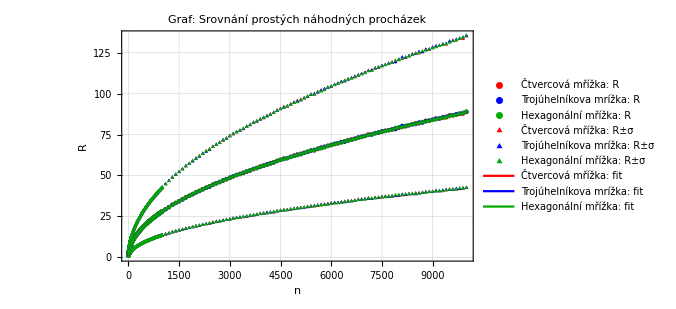

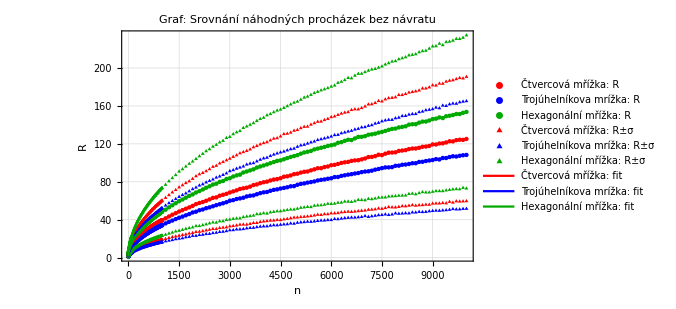

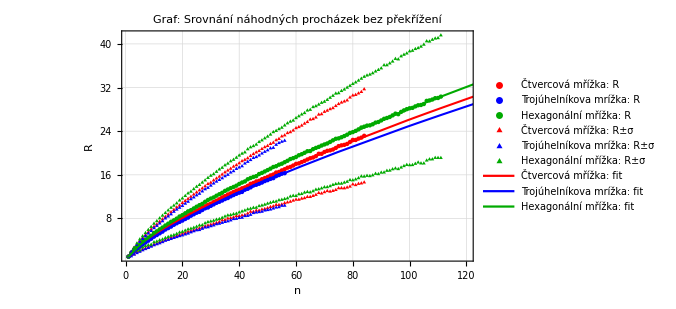

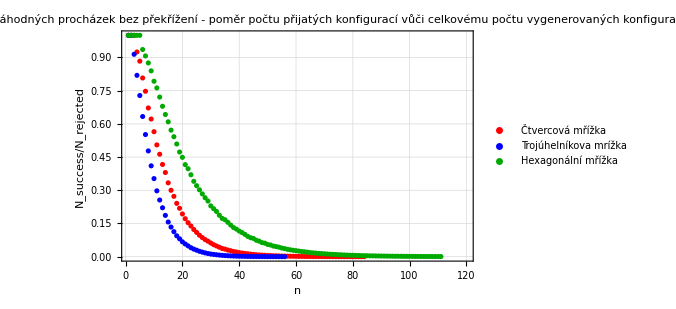

----- Grafy - srovnání různých typů náhodných procházek -----

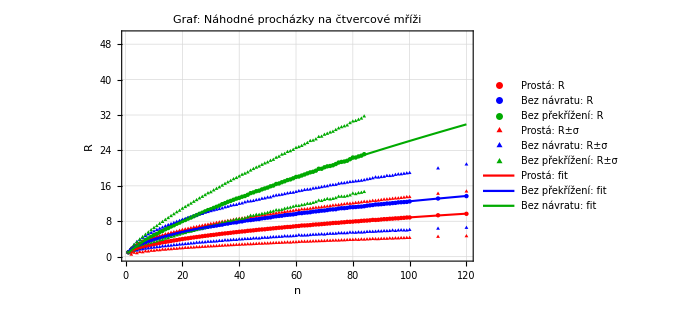

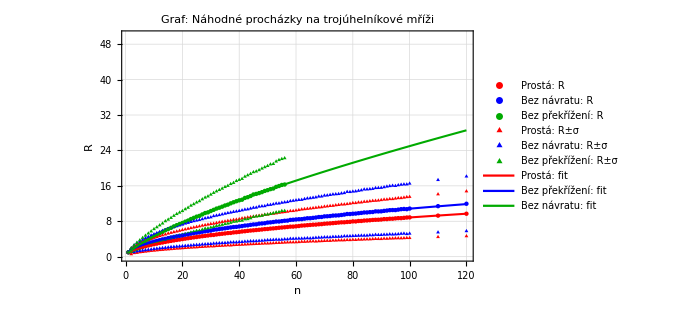

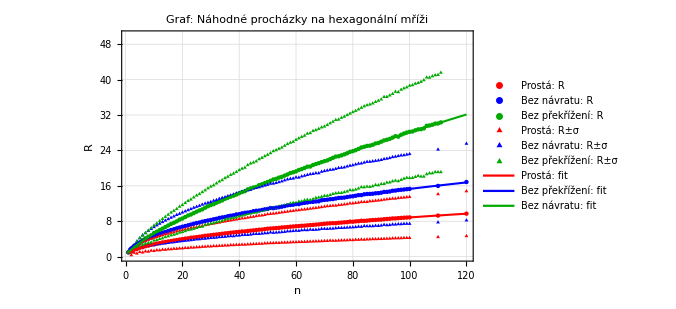

```mathematica
Print["----- Tabulka: Parametry fitu R(n) = c·n^α -----"]
Print[ℝesult]
Print["N.B.: N = počet (přijatých) náhodných procházek, přes které byla počítána průměrná euklidovská vzdálenost od počátku"]

Print["----- Grafy - srovnání náhodných procházek na různých mřížích -----"]
𝔾raphs[[1]]
𝔾raphs[[2]]
𝔾raphs[[3]]
𝔾raphNSuccessVsNRejected

Print["----- Grafy - srovnání různých typů náhodných procházek -----"]
𝔾raphs[[4]]
𝔾raphs[[5]]
𝔾raphs[[6]]
```